```mathematica
Exit[]
```

# Gamma qq PS

```mathematica
<<"/Users/giacomomagni/Documents/Wolfram Mathematica/Sigma.m"
<<"/Users/giacomomagni/Documents/Wolfram Mathematica/HarmonicSums.m"
LaunchKernels[4];
```

Sigma - A summation package by Carsten Schneider — © RISC —  V 2.86 (June 15, 2021)  Help

HarmonicSums by Jakob Ablinger — © RISC — Version 1.0(30/03/21)Help

#### Inputs

```mathematica
here = NotebookDirectory[];
Get[StringJoin[here, "constants.m"]]
```

```mathematica
(* Singlet, large nf exact parts *)
Get[StringJoin[here, "singlet_nf3.m"]]
Get[StringJoin[here, "ns_nf3_nf2.m"]]
(* Singlet, asymptotic N-> Infinity, large nc limit *)
Get[StringJoin[here, "qcd_cusp.m"]]
(* Singlet, moments *)
Get[StringJoin[here, "gqq3nsp.m"]]
Get[StringJoin[here, "gqq3ps.m"]]
Get[StringJoin[here, "gqg3.m"]]
Get[StringJoin[here, "gqg3.m"]]
Get[StringJoin[here, "ggg3.m"]]
```

```mathematica
Get[StringJoin[here, "fitting_utils.m"]]
Get[StringJoin[here, "plotting_utils.m"]]
Get[StringJoin[here, "saving_utils.m"]]
```

```mathematica
thrhigh = 10^-7;
thrlow = 10^-3;
gqqpsmoments = {gqq3psN2,gqq3psN4,gqq3psN6,gqq3psN8};

fsmallN = {1/(n-1)^2, 1/(n-1)^2, SuppLog[n]};
flargeN = {S13m2[n],S13m2[n],S13m2[n]};

(* All the fuctions have to vanish for x->1 *)
fSubLeadingLargeN = {
	{1/(n(n+1)),1/(n(n+1)),1/(n(n+1))},
	{1/(n(n+2)),1/(n(n+2)),1/(n(n+2))}, 
	{1/(n+1)^2,1/(n+1)^2,1/(n+1)^2}, 
	{1/(n+1)^3,1/(n+1)^3,1/(n+1)^3}, 
	{Lm12m1[n],Lm12m1[n],Lm12m1[n]},
	{Lm11m1[n],Lm11m1[n],Lm11m1[n]},
	{S11m2[n],S11m2[n],S11m2[n]},
	{S12m2[n],S12m2[n],S12m2[n]}
	(* {1/(n+1)^4,1/(n+1)^4,1/(n+1)^4}*)
};
fSubLeadingSmallN = {
	{1/n^4,1/n^4,1/n^4},
	{1/n^3,1/n^3,1/n^3},
	{1/n^2,1/n^2,1/n^2},
	{SuppLog[n],SuppLog[n],1}
};
gqq3psasy = MellinInverseSinglet[gqq3psN0asy + gqq3psN1asy + gqq3psNinf] /. Delta[x__] -> 0 /. LimitRules /. ZetaRules;
```

#### Cross candidates

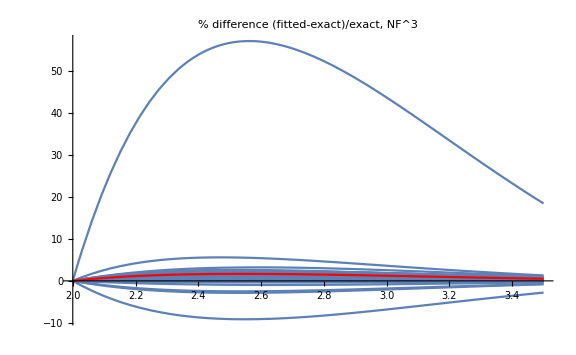

Smooth candidates: 63 out of 66

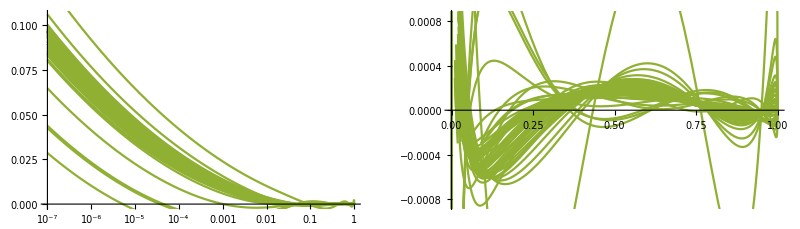

```mathematica
fSubLeadingtot = Join[fSubLeadingSmallN, fSubLeadingLargeN];
gqq3psFittedCross = DoAllFits[fsmallN, flargeN, fSubLeadingtot, gqqpsmoments, gqq3psN0asy, gqq3psN1asy, gqq3psNinf];
PlotRelativeDiffIterate[gqq3psnf3  - Coefficient[gqq3psN0asy+gqq3psN1asy+gqq3psNinf, nf ,3],gqq3psFittedCross,3,2,3.5]
gqq3psinvfull = ListMellinInverse[gqq3psFittedCross];
gqq3psinv = SelectSmoothCandidates[gqq3psinvfull, 4,thrlow,thrlow];
graphQQPSrep = PlotList[gqq3psinv, gqq3psasy, 4, 3] // Show;
graphQQPSlogrep = LogPlotList[gqq3psinv, gqq3psasy, 4, 3] // Show;
GraphicsRow[{graphQQPSlogrep,graphQQPSrep}]
```

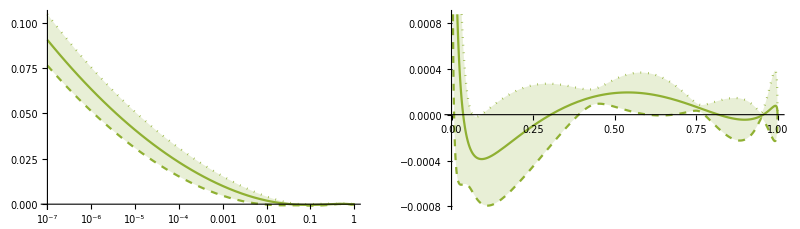

```mathematica
{graphQQPS,graphQQPSlog} =  PlotErrorBand[gqq3psasy, gqq3psinv, 4, 3];
GraphicsRow[{graphQQPSlog,graphQQPS}]
```

#### Cherry Picking

```mathematica
cherryfunctions = {1/n^4, S11m2[n]};
gqq3pscherry = SelectCherriesSpecial[gqq3psFittedCross, cherryfunctions];
gqq3pscherry = SelectSmoothCandidates[gqq3pscherry, 4, thrlow, thrhigh];
```

Selected cherries are: 21 out of 66

Smooth candidates: 19 out of 21

```mathematica
{graphQQPScherry, graphQQPScherrylog} = PlotErrorBand[gqq3psasy, gqq3pscherry, 4, 4]; 
legend = {"cross candidate", "cherries"}; 
GraphicsRow[{
    	ShowLegends[{graphQQPSlog, graphQQPScherrylog}, LogLinearPlot, legend, {3, 4}], 
    	ShowLegends[{graphQQPS, graphQQPScherry}, Plot, legend, {3, 4}]
    	}, ImageSize -> Full
]
```

-Graphics-

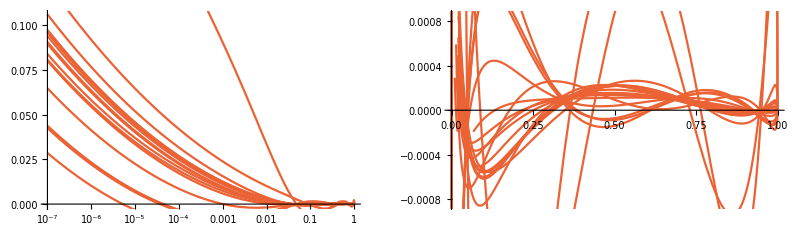

```mathematica
graphQQPScherrylogrep = LogPlotList[gqq3pscherry, gqq3psasy, 4, 4];
graphQQPScherryrep = PlotList[gqq3pscherry, gqq3psasy, 4, 4];
GraphicsRow[{Show[graphQQPScherrylogrep], Show[graphQQPScherryrep]}]
```

#### Plot nf^3

```mathematica
gqq3psasy3 = Coefficient[gqq3psasy, nf, 3];
(*
gqq3psinv3 =  SelectSmoothCandidates[Coefficient[gqq3psinv, nf, 3], 4,thrlow,thrlow];
gqq3psinv3cherries =  SelectSmoothCandidates[Coefficient[gqq3pscherry, nf, 3], 4,thrlow,thrlow];
*)
gqq3psinv3 =  Coefficient[gqq3psinv, nf, 3];
gqq3psinv3cherries =  Coefficient[gqq3pscherry, nf, 3];
gqq3psnf3x = gqq3psnf3x /. QCDConstantsRules //N;
```

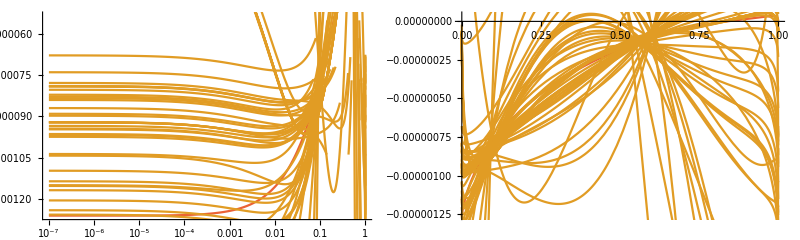

```mathematica
gtmp = PlotList[gqq3psinv3, gqq3psasy3, 4, 2];
gtmplog = LogPlotList[gqq3psinv3, gqq3psasy3, 4, 2];
graphQQPSExa3 = Plot[pifact gqq3psnf3x, {x, 0, 1}, PlotStyle -> clist[[4]], ImageSize->Full];
graphQQPSExa3log = LogLinearPlot[ pifact gqq3psnf3x, {x, 10^-7, 1}, PlotStyle -> clist[[4]], ImageSize->Full];
GraphicsRow[{Show[{graphQQPSExa3log, gtmplog}], Show[{graphQQPSExa3, gtmp}]}, ImageSize->Full]
```

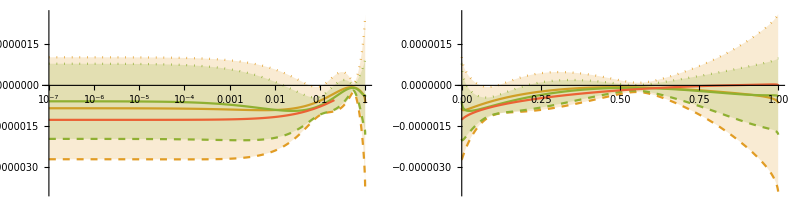

```mathematica
{graphQQPS3, graphQQPS3log} = PlotErrorBand[gqq3psasy3, gqq3psinv3, 4,2];
{graphQQPS3cherry, graphQQPS3cherrylog} = PlotErrorBand[gqq3psasy3, gqq3psinv3cherries, 4,3];
GraphicsRow[{
	Show[graphQQPS3log, graphQQPS3cherrylog, graphQQPSExa3log], 
	Show[graphQQPS3, graphQQPS3cherry, graphQQPSExa3]
	}, ImageSize -> Full
]
```

#### Interpolation checks

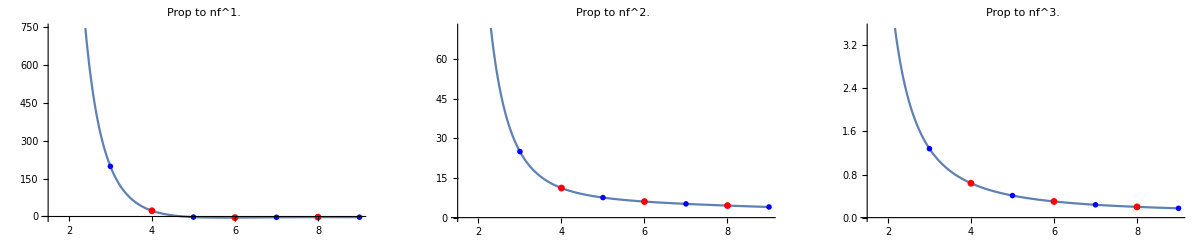

```mathematica
MomentListInterpolator[moments_,nvals_, NF_]:=Module[{momentslist, basis},
		momentslist = Coefficient[moments,nf,NF] //. QCDConstantsRules /. ZetaRules /. InverseHarmonicRules;
		basis ={PolyGamma[0,n-1]/n,PolyGamma[1,n-1]/n, 1/(n-1), n/(n-1)};
		Fit[MapThread[{#1,#2 /. n -> #1} &, {nvals, momentslist}], basis, n]
		(*momentslist[n_] := Indexed[Coefficient[moments,nf,NF] //. QCDConstantsRules /. ZetaRules /. InverseHarmonicRules, IntegerPart[n/2]];
		RationalInterpolation[momentslist[n], {n, 2, 1}, nvals]*)
];

gqq3psasytmp = gqq3psN0asy+ gqq3psN1asy + gqq3psNinf;
GraphicsRow[
	{PlotInterpolation[gqqpsmoments -gqq3psasytmp, {1.1,3,5,7,9}, 1], PlotInterpolation[gqqpsmoments - gqq3psasytmp, {1.5, 3,5,7,9}, 2], PlotInterpolation[gqqpsmoments -gqq3psasytmp, {1.5,3,5,7,9}, 3]}
	, ImageSize->Full, PlotRange->All]
```

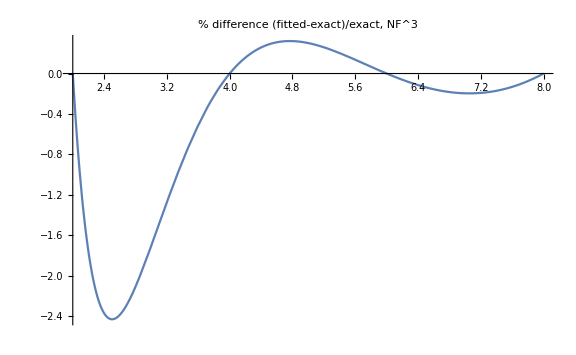

```mathematica
ref = gqq3psnf3 - Coefficient[gqq3psasytmp, nf, 3];
interpolator = MomentListInterpolator[gqqpsmoments - gqq3psasytmp, {2, 4, 6, 8}, 3];
PlotRelativeDiff[ref, nf^3 interpolator, 3, 2, 8]
```

#### Fixing N = 3

```mathematica
flargeN = {{S12m2[n], S11m2[n]},{S12m2[n], S11m2[n]}, {S12m2[n], S11m2[n]}};
fSubLeadingLargeN = {
	{1/(n+1),1/(n+1),1/(n+1)},
	{1/(n+2),1/(n+2),1/(n+2)}, 
	{1/(n+1)^2,1/(n+1)^2,1/(n+1)^2}, 
	{1/(n+1)^3,1/(n+1)^3,1/(n+1)^3}, 
	{Lm12m1[n],Lm12m1[n],Lm12m1[n]},
	{Lm11m1[n],Lm11m1[n],Lm11m1[n]}
};
fSubLeading = Join[fSubLeadingSmallN, fSubLeadingLargeN];

gqq3psFittedInterpol = InterploatedFit[fsmallN, flargeN, fSubLeading, gqqpsmoments, gqq3psN0asy, gqq3psN1asy, gqq3psNinf, {3}];
```

```mathematica
gqq3psinvinterpol = ListMellinInverse[gqq3psFittedInterpol];
gqq3psinvinterpol = SelectSmoothCandidates[gqq3psinvinterpol, 4,thrlow,thrlow];
```

Smooth candidates: 52 out of 55

```mathematica
GraphicsRow[ShowPlots[gqq3psinv, gqq3psinvinterpol, gqq3psasy, 4, {"cross candidates", "N=3"}], ImageSize -> Full]
```

-Graphics-

```mathematica
{graphQQPSint, graphQQPSlogint} =  PlotErrorBand[gqq3psasy, gqq3psinvinterpol, 4, 2];
legend = {"cross candidate", "cherries", "N=3"}; 
GraphicsRow[{
      	ShowLegends[{graphQQPSlog, graphQQPScherrylog, graphQQPSlogint}, LogLinearPlot, legend, {3,4,2}], 
      	ShowLegends[{graphQQPS, graphQQPScherry, graphQQPSint}, Plot, legend, {3,4,2}]
      	}, ImageSize -> Full
  ]
```

-Graphics-

#### Save and final remove

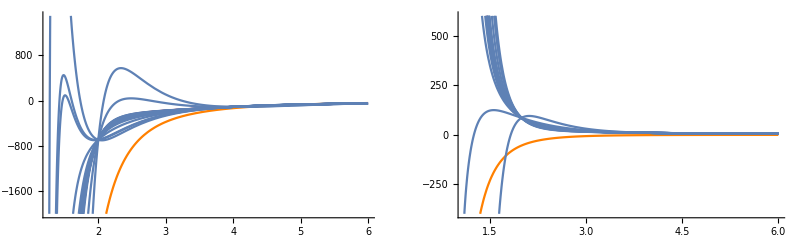

```mathematica
smoothcherryn = gqq3psFittedCross[[Position[gqq3psinvfull, #]& /@ gqq3pscherry //Flatten]] /. largeNrules // Simplify;
gqq3psNasy = gqq3psN0asy + gqq3psN1asy + gqq3psNinf;
g1 = PlotListN[gqq3psNasy, smoothcherryn, 1, -2000, 1500];
g2 = PlotListN[gqq3psNasy, smoothcherryn, 2, -400, 600];
GraphicsRow[{Show[g1, PlotRange-> All],Show[g2, PlotRange-> All]}, ImageSize->Full]
```

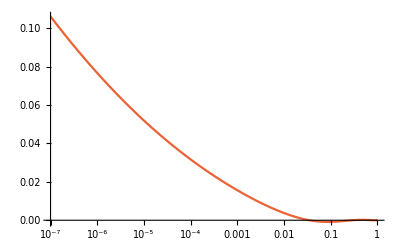
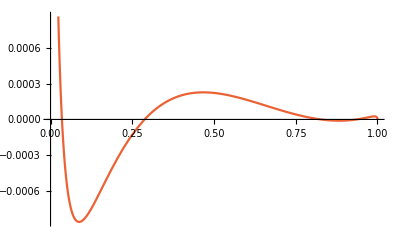
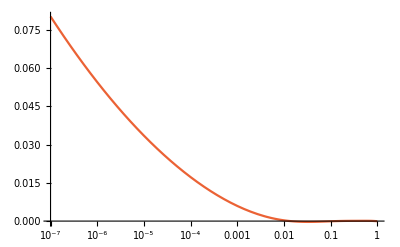
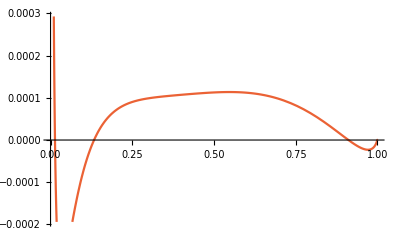
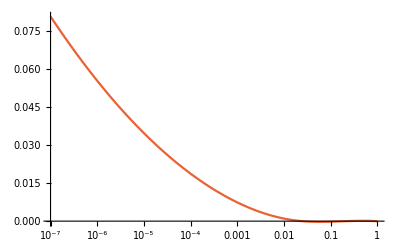
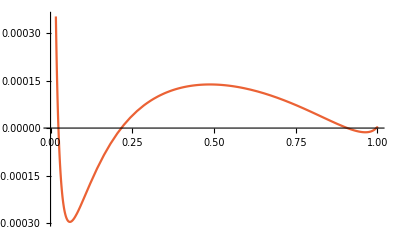
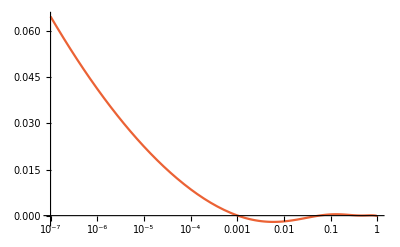
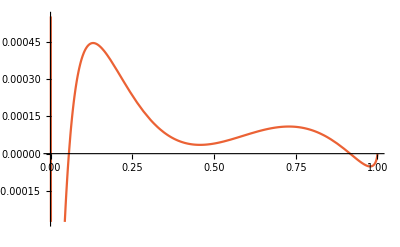
{{1,-Graphics-,-Graphics-},{2,-Graphics-,-Graphics-},{3,-Graphics-,-Graphics-},{4,-Graphics-,-Graphics-},{5,-Graphics-,-Graphics-},{6,-Graphics-,-Graphics-},{7,-Graphics-,-Graphics-},{8,-Graphics-,-Graphics-},{9,-Graphics-,-Graphics-},{10,-Graphics-,-Graphics-},{11,-Graphics-,-Graphics-},{12,-Graphics-,-Graphics-},{13,-Graphics-,-Graphics-},{14,-Graphics-,-Graphics-},{15,-Graphics-,-Graphics-},{16,-Graphics-,-Graphics-},{17,-Graphics-,-Graphics-},{18,-Graphics-,-Graphics-},{19,-Graphics-,-Graphics-}}

```mathematica
MapThread[{#1, #2, #3} &, {Range[1, graphQQPScherrylogrep // Length], graphQQPScherrylogrep, graphQQPScherryrep}]
```

To check 8, 14 and 6

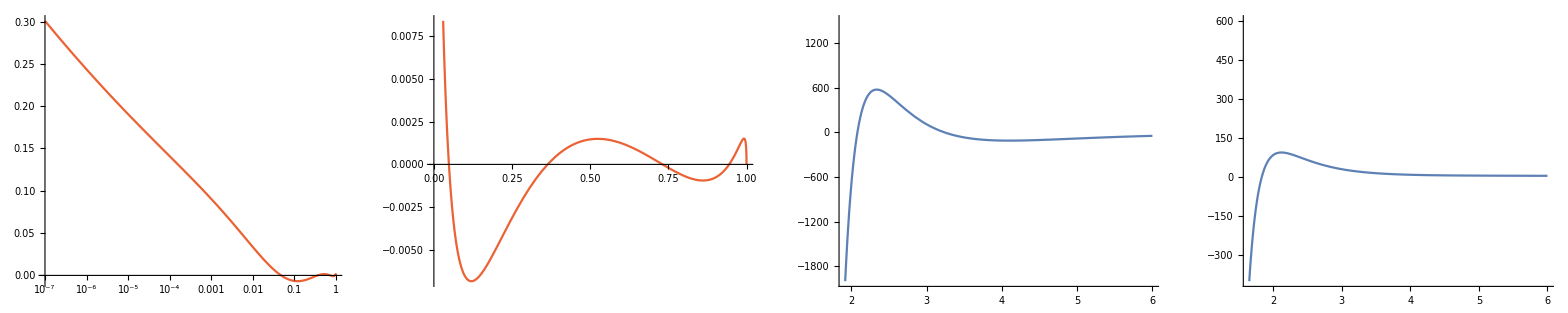

nf (-37994.1/(-1.+n)^2+560405./n^4+109291. Lm12m1[n]+nf (-1636.08/(-1.+n)^2+24737.4/n^4+4672.49 Lm12m1[n]-701.98 S13m2[n])-16771. S13m2[n]+nf^2 (52.1493/n^4-3.89543 Lm12m1[n]+1.12158 S13m2[n]+2.54797 SuppLog[n]))

2.54797 nf^3 (-1+1/x)+109291. nf (1-x) Log[1-x]^2+4672.49 nf^2 (1-x) Log[1-x]^2-3.89543 nf^3 (1-x) Log[1-x]^2+(37994.1 nf Log[x])/x+(1636.08 nf^2 Log[x])/x-93400.9 nf Log[x]^3-4122.89 nf^2 Log[x]^3-8.69155 nf^3 Log[x]^3-16771. nf (-π^4/15-1/2 π^2 Log[1-x] Log[x]+Log[1-x]^3 Log[x]+3/2 Log[1-x]^2 Log[x]^2+3 Log[1-x]^2 PolyLog[2,1-x]+(π^2/2+3 Log[1-x] Log[x]-Log[x]^2/2) PolyLog[2,x]-6 Log[1-x] PolyLog[3,1-x]+3 Log[x] PolyLog[3,1-x]+2 Log[x] PolyLog[3,x]+6 PolyLog[4,1-x]-3 PolyLog[4,x]+6 PolyLog[2,2,x]-3 Log[x] Zeta[3])-701.98 nf^2 (-π^4/15-1/2 π^2 Log[1-x] Log[x]+Log[1-x]^3 Log[x]+3/2 Log[1-x]^2 Log[x]^2+3 Log[1-x]^2 PolyLog[2,1-x]+(π^2/2+3 Log[1-x] Log[x]-Log[x]^2/2) PolyLog[2,x]-6 Log[1-x] PolyLog[3,1-x]+3 Log[x] PolyLog[3,1-x]+2 Log[x] PolyLog[3,x]+6 PolyLog[4,1-x]-3 PolyLog[4,x]+6 PolyLog[2,2,x]-3 Log[x] Zeta[3])+1.12158 nf^3 (-π^4/15-1/2 π^2 Log[1-x] Log[x]+Log[1-x]^3 Log[x]+3/2 Log[1-x]^2 Log[x]^2+3 Log[1-x]^2 PolyLog[2,1-x]+(π^2/2+3 Log[1-x] Log[x]-Log[x]^2/2) PolyLog[2,x]-6 Log[1-x] PolyLog[3,1-x]+3 Log[x] PolyLog[3,1-x]+2 Log[x] PolyLog[3,x]+6 PolyLog[4,1-x]-3 PolyLog[4,x]+6 PolyLog[2,2,x]-3 Log[x] Zeta[3])

```mathematica
posix = 8;
GraphicsRow[{LogPlotList[gqq3pscherry, gqq3psasy, 4, 4][[posix]], PlotList[gqq3pscherry, gqq3psasy, 4, 4][[posix]], g1[[posix+1]], g2[[posix+1]]}, ImageSize->Full]
smoothcherryn[[posix]]
gqq3pscherry[[posix]]
```

Remove 14 and 8

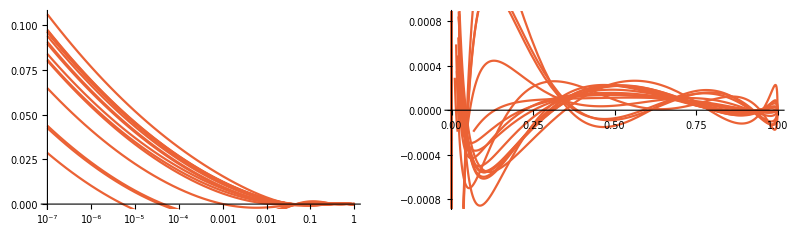

```mathematica
gqq3pscherryrefined = Delete[gqq3pscherry,14];
gqq3pscherryrefined = Delete[gqq3pscherryrefined,8];
graphQQPScherrylogrepref = LogPlotList[gqq3pscherryrefined, gqq3psasy, 4, 4];
graphQQPScherryrepref = PlotList[gqq3pscherryrefined, gqq3psasy, 4, 4];
GraphicsRow[{Show[graphQQPScherrylogrepref], Show[graphQQPScherryrepref]}]
```

```mathematica
{graphQQPScherry, graphQQPScherrylog} = PlotErrorBand[gqq3psasy,gqq3pscherryrefined, 4, 4]; 
legend = {"cross candidate", "cherries"}; 
GraphicsRow[{
    	ShowLegends[{graphQQPSlog, graphQQPScherrylog}, LogLinearPlot, legend, {3, 4}], 
    	ShowLegends[{graphQQPS, graphQQPScherry}, Plot, legend, {3, 4}]
    	}, ImageSize -> Full
]
```

-Graphics-

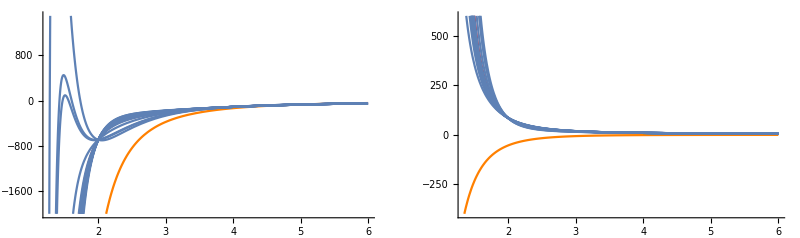

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/gqq3psnf1.c

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/gqq3psnf2.c

```mathematica
smoothcherryn = gqq3psFittedCross[[Position[gqq3psinvfull, #] & /@ gqq3pscherryrefined // Flatten]] /. largeNrules // Simplify;
g1ref = PlotListN[gqq3psNasy, smoothcherryn, 1, -2000, 1500];
g2ref = PlotListN[gqq3psNasy, smoothcherryn, 2, -400, 600];
GraphicsRow[{Show[g1ref, PlotRange -> All], Show[g2ref, PlotRange -> All]}, ImageSize -> Full] 
exportMeList[gqq3psNasy, smoothcherryn, StringJoin[storepath, "gqq3psnf1.c"], 1];
exportMeList[gqq3psNasy, smoothcherryn, StringJoin[storepath, "gqq3psnf2.c"], 2];
```

```mathematica
smoothcherryn//Length
```

17